```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/quantum_stochastic/math

```mathematica
MiyamotoData=Import["delNSqSample.csv"];
```

```mathematica
dN2vsNb=Map[{#[[1]],#[[4]]}&,Drop[MiyamotoData,1]];
```

```mathematica
NbList=dN2vsNb[[All,1]];
```

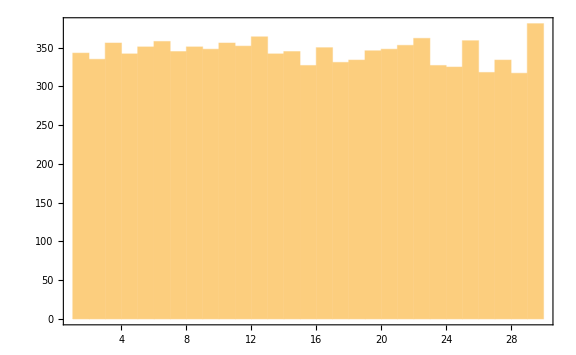

```mathematica
Histogram[NbList]
```

```mathematica
dN=1;
Nbmin=2;
Nmax=29;
```

```mathematica
binning[Nb_]:=Select[dN2vsNb,Nb-dN/2<=#[[1]]<Nb+dN/2&];
```

```mathematica
dN2List=Table[bindata=binning[Nb];
{Nb,If[Length[bindata]>1,Mean[bindata[[All,2]]]±Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],10^-3],0]},{Nb,Nbmin,Nmax,dN}];
```

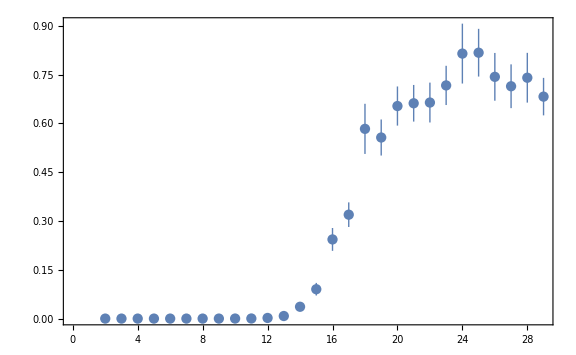

```mathematica
ListPlot[dN2List,Joined->False]
```

```mathematica
dN2we=Table[bindata=binning[Nb];
If[Length[bindata]>1,{Nb,Mean[bindata[[All,2]]],Max[StandardDeviation[bindata[[All,2]]]/Sqrt[Length[bindata[[All,2]]]],10^-3]},None],{Nb,Nbmin,Nmax,dN}];
```

```mathematica
weights=1/dN2we[[All,3]]^2;
```

```mathematica
LegendreP[0,x]
```

1

```mathematica
f[x_]=c/(1+Exp[-a0 LegendreP[0,x]-a1 LegendreP[1,x](*-a2 LegendreP[2,x]-a3 LegendreP[3,x]-a4 LegendreP[4,x]-a5 LegendreP[5,x]*)]);
```

```mathematica
fit=NonlinearModelFit[dN2we[[All,{1,2}]],f[x],{a0,a1(*,a2,a3,a4,a5*),c},x,Weights->weights]
```

FittedModel[0.701247/(1+ⅇ^(«18»-«19» x))]

```mathematica
BestFit[x_]=fit["BestFit"]
bands2s[x_]=fit["MeanPredictionBands"];
```

0.701247/(1+ⅇ^(19.0888-1.12977 x))

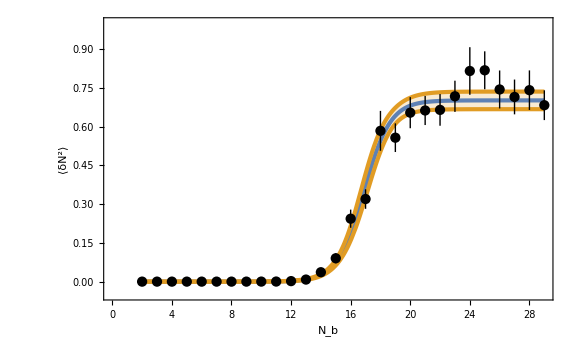

```mathematica
Show[Plot[{BestFit[x],bands2s[x]},{x,Nbmin,Nmax},Filling->{2->{1}},PlotRange->{-0.05,1},FrameLabel->{Subscript[N, "b"],"⟨δN^2⟩"}],ListPlot[dN2List,Joined->False,PlotStyle->Black]]
```

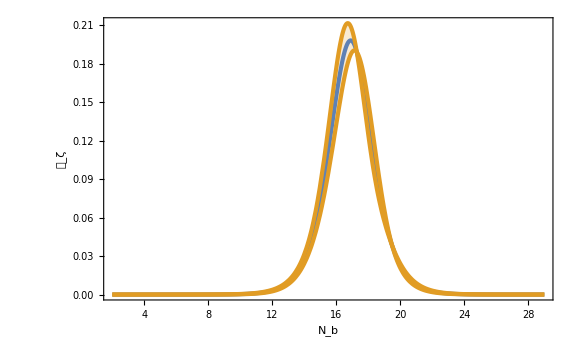

```mathematica
Plot[{BestFit'[x],bands2s'[x]},{x,Nbmin,Nmax},PlotRange->Full,Filling->{2->{1}},FrameLabel->{Subscript[N, "b"],Subscript[𝒫, ζ]}]
```